```mathematica
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
L2[n_,1,c_]:=L2[n,1,c]=(1/den[c])Sum[alpha[j,c]Log[j/den[c]],{j,den[c]+1,den[c] n}];L2[n_,0,c_]:=0
L2[n_,k_,c_]:=L2[n,k,c]=(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]L2[den[c] n/j,k-1,c]],{j,den[c]+1,den[c] n}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
L1[n_,z_,c_]:=Sum[bin[z,k] L2[n,k,c],{k,0,Floor[Log[c,n]]}]
zeros[n_, c_]:=List@@Roots[L1[n,z,c]-1==0,z][[All,2]]
L1Alt[ n_, z_, c_] := 1-Product[ 1-z/r,{r,zeros[n,c]}]
L1m[ n_, c_] := 1-Product[ 1+r^-1,{r,zeros[n,c]}]
```

```mathematica
Expand[N[L1[100,z,4/3]]]
```

1.-3.84024 z+6.34645 z^2-6.32933 z^3+2.83562 z^4+0.0783242 z^5+0.14543 z^6-0.150889 z^7+0.0386438 z^8-0.00777589 z^9+0.00118332 z^10-0.000115508 z^11+7.29511×10^-6 z^12-2.95732×10^-7 z^13+8.80027×10^-9 z^14-1.81087×10^-10 z^15+1.37187×10^-12 z^16

```mathematica
N[Log[2,100]]
```

6.64386

```mathematica
N[Log[4/3,100]]
```

```mathematica
N[L1Alt[ 100, -1, 3/2]]
```

9.95352-6.57473×10^-16 ⅈ

```mathematica
N[L1[100,-1,3/2]]
```

9.95352

```mathematica
N[L1m[100,3/2]]
```

9.95352-6.57473×10^-16 ⅈ

```mathematica
p[n_,j_,k_]:=If[n<j,0,1/k-p[n/j,2,k+1]+p[n,j+1,k]]
pi[n_] := Sum[ MoebiusMu[j]j^-1p[n^(1/j),2,1],{j,1,Log[2,n]}]
```

```mathematica
pi[100]
```

25

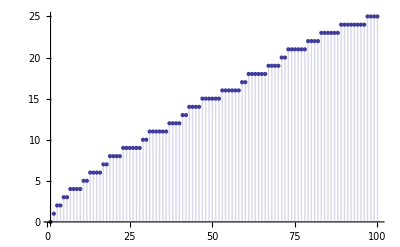

```mathematica
DiscretePlot[pi[n],{n,1,100}]
```

```mathematica
(-1)^k Binomial[ -1,k]/.k->3
```

1

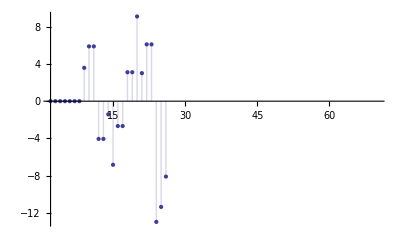

```mathematica
DiscretePlot[ FullSimplify[D[ L1[ n, z, 3],{z,2}]], {n,2,70}]//TableForm
```